## Kapitola 10 - RBF síť a Iris data

Demonstrace použití RBF sítě na datech z databáze UCI.

## Inicializace knihovny NeuralNetworks

Nejprve načteme knihovnu pro neuronové sítě.

```mathematica
<<NeuralNetworks`
```

Pokud pracujete v Mathematice 8.0, vypněte ještě zobrazování chybové hlášky Remove::rmnsm. Tuto hlášku vyhazují funkce knihovny NeuralNetworks. Na funkci knihovny toto nemá žádný vliv.

```mathematica
Off[Remove::rmnsm];
```

## Import dat

### Načtení dat ze souboru

Nastavíme si pracovní adresář na ten, kde máme uložen aktuální notebook, načítaná data musejí být ve stejném adresáři.

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Dokumenty\BP

A načteme data.

```mathematica
data=Import["iris.data"];
```

### Načtení dat přímo z internetu

Jiná možnost je importovat data přímo z internetu - příklad pro UCI databázi (stejná data jako v předchozím příkladu - načtení dat ze souboru).

```mathematica
data=Import["http://ftp.ics.uci.edu/pub/machine-learning-databases/iris/iris.data"];
```

## Předzpracování dat

Předzpravování dat provedeme pomocí stejného postupu, který je popsán v kapitole 5 - Dopředná síť a Iris data.

```mathematica
data2=Drop[data,-1];
inData=data2[[All,1;;4]];(*vstupní parametry*)
outDataTmp=data2[[All,5]];(*výstupní parametr*)
outVal=Tally[outDataTmp][[All,1]];
encode=MapIndexed[#1->Normal[SparseArray[#2->1,{Length[outVal]}]]&,outVal];
outData=Flatten[outDataTmp]/.encode;
```

## Zpracování dat neuronovou sítí

Inicializace sítě - zadáme trénovací množinu, rozdělenou na vstupní a výstupní data, počet neuronů, případně můžeme zadat i aktivační funkci neuronu. Počet neuronů se zadává jako kladné celé číslo.

Vytvořenou síť si uložíme do proměnné "net".

```mathematica
net=InitializeRBFNet[inData,outData,4,Neuron->Sigmoid]
```

RBFNet[{{w1, λ, w2}, χ},{Neuron → Sigmoid, FixedParameters → None, AccumulatedIterations → 0, CreationDate → {2011, 5, 13, 9, 1, 36.5484849}, OutputNonlinearity → None, NumberOfInputs → 4}]

Můžeme si nechat zobrazit nějaké další informace o vytvořené síti.

```mathematica
NetInformation[net]
```

Radial Basis Function network. Created 2011-5-13 at 9:01. The network has 4 inputs and 3 outputs.  It consists of 4 basis functions of Sigmoid type. The network has a linear submodel.

Natrénujeme síť pomocí funkce "NeuralFit", které zadáme naší síť (proměnná "net"), trénovací množinu ("inData" a "outData") a počet učících kroků.

Funkce NeuralFit vyprodukuje naučenou síť a záznam o průběhu učení (může se hodit) - obě tyto návratové hodnoty si ukládáme (do proměnné "net2" a "record").

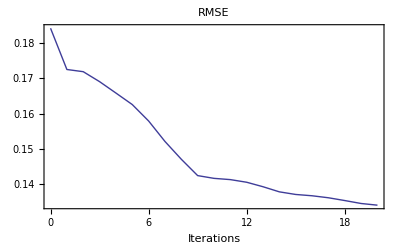

```mathematica
{net2,record}=NeuralFit[net,inData,outData,20];
```

Máme síť naučenou a můžeme se podívat na to, jak odpovídala během učení. Síť má 3 výstupy, proto následující příkaz vyprodukuje 3 grafy. Kadždý graf ukazuje počet správně a špatně klasifikovaných dat dané třídy v průběhu učení.

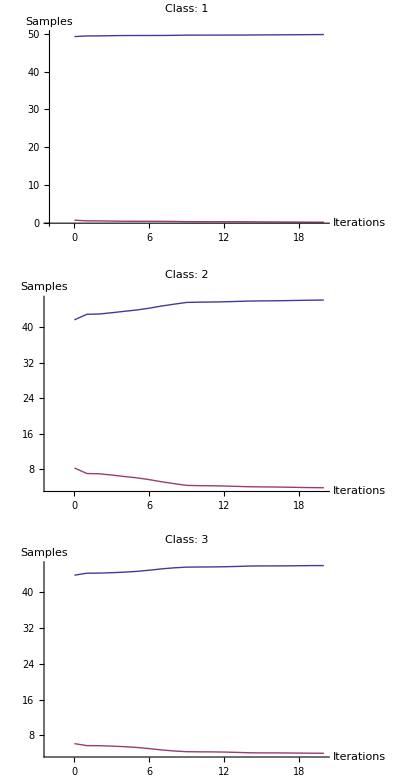

```mathematica
NetPlot[record,inData,outData,DataFormat->ClassPerformance]
```

Můžeme se podívat na klasifikaci pomocí "data/model" diagramu. Graf je interaktivní - pomocí myši ho můzeme otáčet, posouvat (Shift + myš) a zoomovat (Ctrl + myš). Čím víšší hodnoty jsou na diagonále, tím vyšší je úspěšnost klasifikace.

```mathematica
NetPlot[net2,inData,outData,DataFormat->BarChart]
```

-Graphics3D-

Síť je možné si nechat symbolicky vyhodnotit - pro větší sítě je to ale už zcela nepřehledné, nicméně aktivační funkce tam zcela jistě poznáte.

Síť funguje v Mathematice jako klasická funkce, takže ji můžeme dávat parametry - včetně symbolů.

```mathematica
net2[{x1,x2,x3,x4}]
```

{-18.6379+4.3593/(1+ⅇ^(0.166135 (-5.12717+x1)^2+0.166135 (-1.90397+x2)^2+0.166135 (-6.33436+x3)^2+0.166135 (-3.11743+x4)^2))+122.429/(1+ⅇ^(0.0154206 (-8.43765+x1)^2+0.0154206 (-2.98333+x2)^2+0.0154206 (-1.3835+x3)^2+0.0154206 (-2.1264+x4)^2))-13.4602/(1+ⅇ^(0.0579903 (-5.09324+x1)^2+0.0579903 (-2.20537+x2)^2+0.0579903 (-6.97779+x3)^2+0.0579903 (-1.75702+x4)^2))-70.4776/(1+ⅇ^(0.0231133 (-7.96802+x1)^2+0.0231133 (-3.20416+x2)^2+0.0231133 (-2.42941+x3)^2+0.0231133 (-0.524327+x4)^2))-0.791442 x1+0.136367 x2+1.69279 x3-1.65736 x4,426.749-10.6917/(1+ⅇ^(0.166135 (-5.12717+x1)^2+0.166135 (-1.90397+x2)^2+0.166135 (-6.33436+x3)^2+0.166135 (-3.11743+x4)^2))-2992.99/(1+ⅇ^(0.0154206 (-8.43765+x1)^2+0.0154206 (-2.98333+x2)^2+0.0154206 (-1.3835+x3)^2+0.0154206 (-2.1264+x4)^2))+29.8417/(1+ⅇ^(0.0579903 (-5.09324+x1)^2+0.0579903 (-2.20537+x2)^2+0.0579903 (-6.97779+x3)^2+0.0579903 (-1.75702+x4)^2))+1974.01/(1+ⅇ^(0.0231133 (-7.96802+x1)^2+0.0231133 (-3.20416+x2)^2+0.0231133 (-2.42941+x3)^2+0.0231133 (-0.524327+x4)^2))+11.3944 x1-4.67395 x2-25.4362 x3+36.0718 x4,-407.111+6.33245/(1+ⅇ^(0.166135 (-5.12717+x1)^2+0.166135 (-1.90397+x2)^2+0.166135 (-6.33436+x3)^2+0.166135 (-3.11743+x4)^2))+2870.56/(1+ⅇ^(0.0154206 (-8.43765+x1)^2+0.0154206 (-2.98333+x2)^2+0.0154206 (-1.3835+x3)^2+0.0154206 (-2.1264+x4)^2))-16.3815/(1+ⅇ^(0.0579903 (-5.09324+x1)^2+0.0579903 (-2.20537+x2)^2+0.0579903 (-6.97779+x3)^2+0.0579903 (-1.75702+x4)^2))-1903.53/(1+ⅇ^(0.0231133 (-7.96802+x1)^2+0.0231133 (-3.20416+x2)^2+0.0231133 (-2.42941+x3)^2+0.0231133 (-0.524327+x4)^2))-10.603 x1+4.53758 x2+23.7434 x3-34.4145 x4}

V následující kapitole se podíváme podrobněji na metody učení sítě.

## Prohlášení

Tento text je součástí bakalářské práce Adama Činčury “Demonstrační aplikace pro podporu kurzu neuronových sítí” na FEL ČVUT 2011. Vznikl úpravou textu Petra Chlumského.